## Prelab 6 Francesco Vassalli

### Q1 See Appendix

### Q2 See Appendix

### Q3

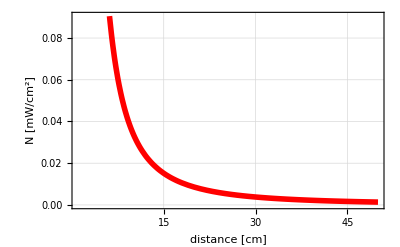

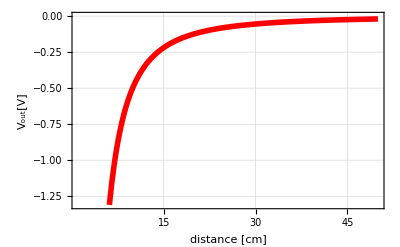

```mathematica
num[r_]:=700/(683*.3*r^2);
Plot[num[r],{r,1,50},Frame->True,Axes->True,
LabelStyle->{FontFamily->"Arial", FontSize->13},
FrameLabel->{"distance [cm]","N [mW/cm^2]"},
FrameStyle->Thickness[.005],PlotStyle->{Red,Thickness[.01]},GridLines->Automatic]
R940=10;
Rf=1.8*10^6;
vout[r_]:=-1*.8*R940*Rf*num[r]*10^-6;
Plot[vout[r],{r,1,50},Frame->True,Axes->True,
LabelStyle->{FontFamily->"Arial", FontSize->13},
FrameLabel->{"distance [cm]","V_out[V]"},
FrameStyle->Thickness[.005],PlotStyle->{Red,Thickness[.01]},GridLines->Automatic]
```

The loop law allows us to calculate the voltage drop at each point in	LED emitter loop.

10-1.9-20*10^-3(50+R_s)=0

This makes R_s=355Ω.

### Q4

I think making the predictions have good modeling of the light will be hard as there are a lot of variables to control. I have a lot of equations on how photodiodes work considering we haven’t covered them at all in lecture.